# Matematična umetnost: Generiranje slik s formulami

Ta projekt prikazuje, kako lahko z matematičnimi formulami ustvarimo različne oblike in slike v okolju Mathematica. Pri tem uporabimo klasične primere, kot so Mandelbrotova množica, Barnsleyjev praprotni fraktal, parametrične krivulje in podatke iz Excel datoteke. Namen projekta je pokazati tako matematično ozadje kot tudi vizualne učinke.

## Formule:

Mandelbrotova množica:   z_(n+1)=z_n^2+c
Parametrične krivulje: x(t) = f_1(t), y(t) = f_2(t)
Barnsleyjev praproti fraktal: Afinske transformacije z različnimi verjetnostmi

## 1. Mandelbrotova množica

Implementacija Mandelbrotove množice kot osnovni primer kompleksne dinamike.

```mathematica
mandelbrotPlot=Rasterize[DensityPlot[mandelbrotCompiled[x,y,100],{x,-2,1},{y,-1.5,1.5},PlotPoints->400,ColorFunction->"SunsetColors",Mesh->False,Frame->False]];
```

```mathematica
mandelbrotPlot
```

-Graphics-

## 2. Animacija Mandelbrotove množice

S pomočjo ListAnimate lahko ustvarim animacijo, kjer se število iteracij povečuje . Tako dobimo občutek, kako kompleksnost fraktala raste .

```mathematica
frames=Table[DensityPlot[mandelbrotCompiled[x,y,50+i],{x,-2,1},{y,-1.5,1.5},PlotPoints->200,ColorFunction->"DeepSeaColors",Frame->False],{i,0,50,5}];
```

```mathematica
ListAnimate[frames]
```

## 3. Parametrične krivulje

Z uporabo sinusnih in kosinusnih funkcij ustvarim estetske parametrične krivulje, ki so pogosto videti kot cvetovi ali geometrijski vzorci.

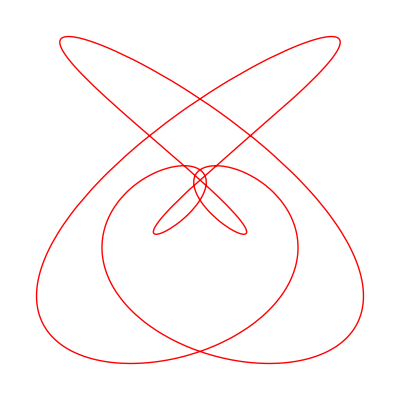

```mathematica
curvePlot=ParametricPlot[{Sin[3 t]+Cos[5 t],Sin[4 t]-Cos[2 t]},{t,0,2 π},PlotStyle->{Thick,Red},Axes->False,AspectRatio->1]
```

## 4. Interaktivna vizualizacija parametričnih krivulj

Z uporabo funkcije Manipulate lahko spreminjam parametre parametričnih funkcij in s tem interaktivno raziskujem različne oblike.

```mathematica
Manipulate[ParametricPlot[{Sin[a t]+Cos[b t],Sin[c t]-Cos[d t]},{t,0,2 π},PlotStyle->{Thick,Blue},Axes->False,AspectRatio->1],{{a,3},1,10,1},{{b,5},1,10,1},{{c,4},1,10,1},{{d,2},1,10,1}]
```

## 5. Uvoz podatkov iz Excela in analiza

Podatke iz Excel datoteke uporabimo za prikaz parametrične krivulje. Na ta način povezujem matematično obdelavo podatkov z vizualizacijo.

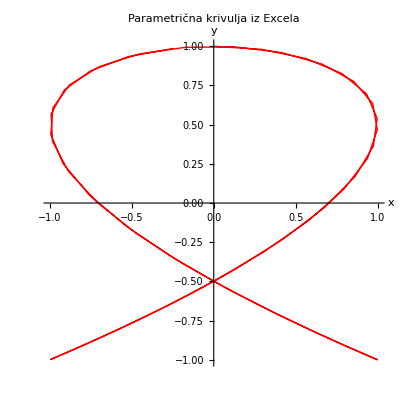

```mathematica
excelDatoteka=FileNameJoin[{NotebookDirectory[],"projekt_podatki.xlsx"}];
dataParam=Import[excelDatoteka,{"Sheets","Parametric"}];
dataMatrix=Import[excelDatoteka,{"Sheets","Matrix"}];
paramMatrika=Rest[dataParam];
ListLinePlot[paramMatrika[[All,{2,3}]],PlotStyle->{Thick,Red},AspectRatio->1,AxesLabel->{"x","y"},PlotLabel->"Parametrična krivulja iz Excela"]
```

## 6. Barvni vzorec iz Excela

Prikažem matriko števil kot barvno sliko in izračunam povprečja po vrsticah matrike.

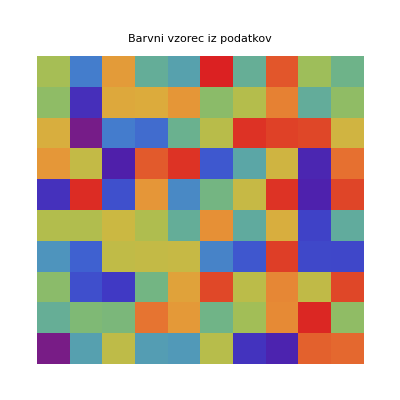

```mathematica
matrixVals=Rest[dataMatrix];
matrixVals=matrixVals[[All,1;;10]];
ArrayPlot[matrixVals,ColorFunction->"Rainbow",PlotLabel->"Barvni vzorec iz podatkov"]
```

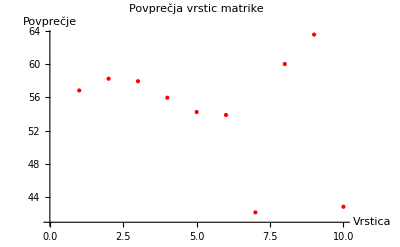

```mathematica
rowMeans=Mean/@matrixVals;
ListPlot[rowMeans,PlotStyle->{Red,PointSize[Medium]},PlotLabel->"Povprečja vrstic matrike",AxesLabel->{"Vrstica","Povprečje"}]
```

## 7. Barnsleyjev praproti fraktal

Barnsleyjev praproti fraktal je generiran z afinskimi transformacijami z določenimi verjetnostmi. To ustvari realistično simulacijo listov praproti.

```mathematica
Manipulate[Module[{x=0.,y=0.,points={},r},Do[r=RandomReal[];{x,y}=Which[r<0.01,{0,0.16 y},r<0.86,{0.85 x+0.04 y,-0.04 x+0.85 y+1.6},r<0.93,{0.2 x-0.26 y,0.23 x+0.22 y+1.6},True,{0.28 y-0.15 x,0.26 x+0.24 y+0.44}];AppendTo[points,{x,y}],{n}];Graphics[{Directive[color,PointSize[size]],Point[points]},PlotRange->{{-3,3},{0,10}},Background->White]],{{n,10000},1000,100000,1000},{{size,0.001},0.0001,0.005,Appearance->"Labeled"},{{color,Green},{Green,Blue,Red,Purple,Darker[Green]}}]
```